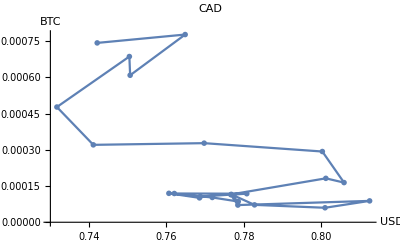

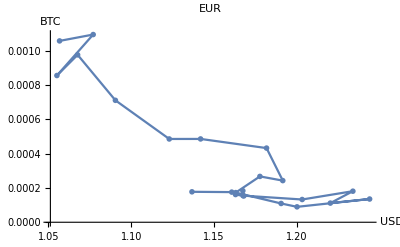

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data3= {curr1[[All,7]],curr2[[All,8]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data3->data3,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"CAD", AxesLabel->{"USD","BTC"}]

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data4 = {curr1[[All,11]],curr2[[All,12]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data4->data4,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"EUR", AxesLabel->{"USD","BTC"}]
```

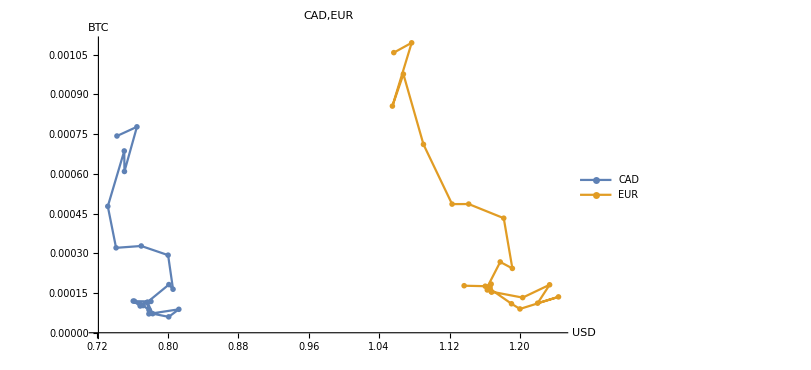

```mathematica
ListPlot[{data3,data4},Joined->True, PlotRange->All,PlotLegends-> {"CAD","EUR"}, PlotLabel->"CAD,EUR", AxesLabel->{"USD","BTC"},ImageSize->600,PlotMarkers->{●}]
```

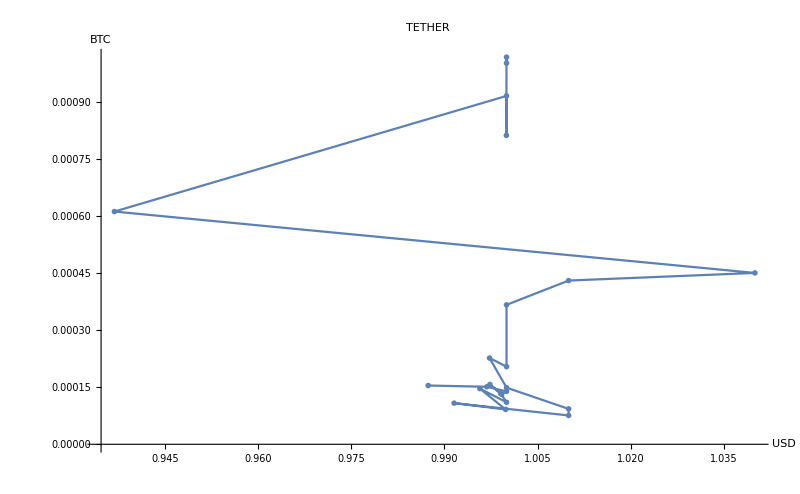

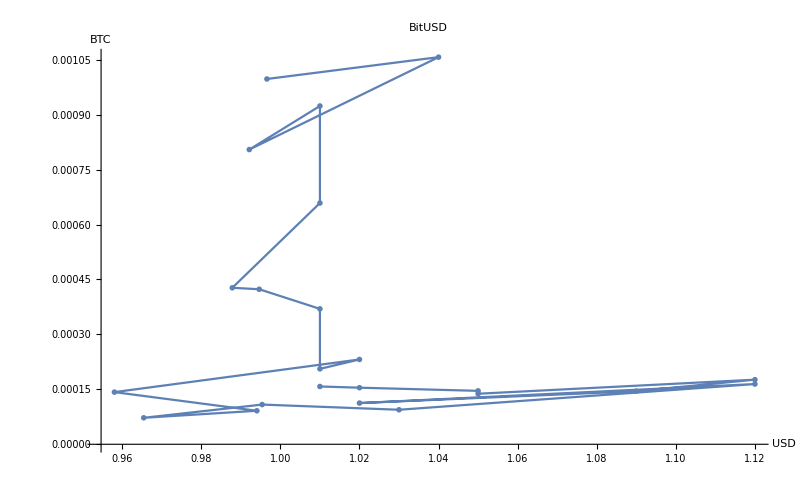

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data5 = {curr1[[All,21]],curr2[[All,22]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data5->data5,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"TETHER", AxesLabel->{"USD","BTC"}]

curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data6 = {curr1[[All,23]],curr2[[All,24]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data6->data6,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"BitUSD", AxesLabel->{"USD","BTC"}]
```

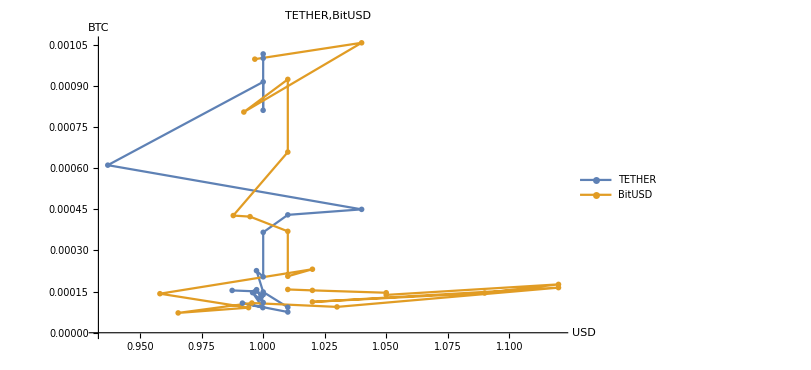

```mathematica
ListPlot[{data5,data6},Joined->True, PlotRange->All,PlotLegends-> {"TETHER","BitUSD"}, PlotLabel->"TETHER,BitUSD", AxesLabel->{"USD","BTC"},ImageSize->600,PlotMarkers->{●}]
```

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data3= {curr1[[All,7]],curr2[[All,8]]}//Transpose;
labels = curr1[[All,1]];
ListPlot[data3->data3,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"CAD", AxesLabel->{"USD","BTC"}]
```

-Graphics-

```mathematica
anArray=curr2[[All,7]]
```

{0.7621,0.7808,0.7688,0.7686,0.7607,0.7719,0.7786,0.7767,0.7785,0.8125,0.801,0.7828,0.7768,0.8012,0.8059,0.8003,0.7698,0.7412,0.7318,0.7505,0.7507,0.7649,0.7422}

```mathematica
newColumn=anArray-0.7621
```

{0.,0.0187,0.0067,0.0065,-0.0014,0.0098,0.0165,0.0146,0.0164,0.0504,0.0389,0.0207,0.0147,0.0391,0.0438,0.0382,0.0077,-0.0209,-0.0303,-0.0116,-0.0114,0.0028,-0.0199}

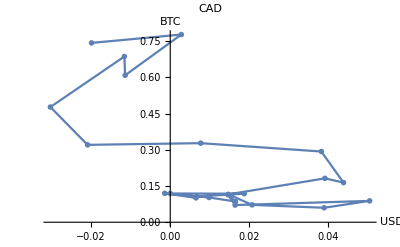

```mathematica
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data3= {newColumn,curr2[[All,8]]*1000}//Transpose;
labels = curr1[[All,1]];
ListPlot[data3->data3,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"CAD", AxesLabel->{"USD","BTC"}]
```

{1.1366,1.1606,1.1629,1.1679,1.1673,1.1674,1.2031,1.2337,1.2201,1.2438,1.2,1.1904,1.163,1.1776,1.1914,1.1816,1.1418,1.1229,1.0904,1.0676,1.0551,1.077,1.0567}

{0.,0.024,0.0263,0.0313,0.0307,0.0308,0.0665,0.0971,0.0835,0.1072,0.0634,0.0538,0.0264,0.041,0.0548,0.045,0.0052,-0.0137,-0.0462,-0.069,-0.0815,-0.0596,-0.0799}

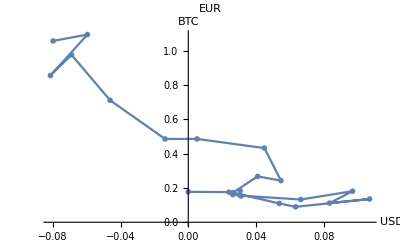

```mathematica
newColumn1 =curr1[[All,11]]
newColumn1=newColumn1-1.1366
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data4 = {newColumn1,curr2[[All,12]]*1000}//Transpose;
labels = curr1[[All,1]];
ListPlot[data4->data4,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"EUR", AxesLabel->{"USD","BTC"}]
```

{1.01,1.02,1.05,1.05,1.12,1.09,1.02,1.12,1.03,0.99539,0.965446,0.994058,0.958033,1.02,1.01,1.01,0.994654,0.987841,1.01,1.01,0.992133,1.04,0.996592}

{0.01,0.02,0.05,0.05,0.12,0.09,0.02,0.12,0.03,-0.00461,-0.034554,-0.005942,-0.041967,0.02,0.01,0.01,-0.005346,-0.012159,0.01,0.01,-0.007867,0.04,-0.003408}

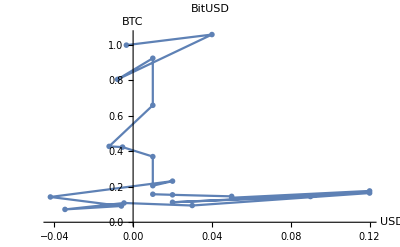

```mathematica
newColumn2=curr1[[All,23]]
newColumn2=newColumn2-1
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data6 = {newColumn2,curr2[[All,24]]*1000}//Transpose;
labels = curr1[[All,1]];
ListPlot[data6->data6,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"BitUSD", AxesLabel->{"USD","BTC"}]
```

{0.987386,0.996818,1,0.999215,0.997323,0.999088,1,0.995702,0.999847,0.991558,1.01,1.01,1,0.997266,1,1,1.01,1.04,0.936855,1,0.999972,0.999997,1}

{-0.012614,-0.003182,0,-0.000785,-0.002677,-0.000912,0,-0.004298,-0.000153,-0.008442,0.01,0.01,0,-0.002734,0,0,0.01,0.04,-0.063145,0,-0.000028,-3.×10^-6,0}

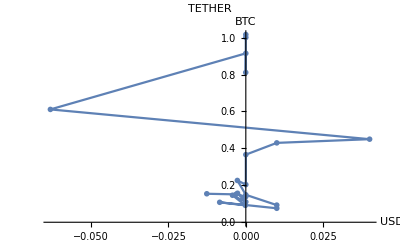

```mathematica
newColumn3=curr1[[All,21]]
newColumn3=newColumn3-1
curr1=Import[NotebookDirectory[]<>"newdata.csv"];
curr2=Import[NotebookDirectory[]<>"newdata.csv"];
curr1=Take[curr1,-23];
curr2=Take[curr2,-23];
data5 = {newColumn3,curr2[[All,22]]*1000}//Transpose;
labels = curr1[[All,1]];
ListPlot[data5->data5,Joined->True,LabelingFunction->Automatic,PlotRange->All, PlotMarkers->{●}, PlotLabel->"TETHER", AxesLabel->{"USD","BTC"}]
```

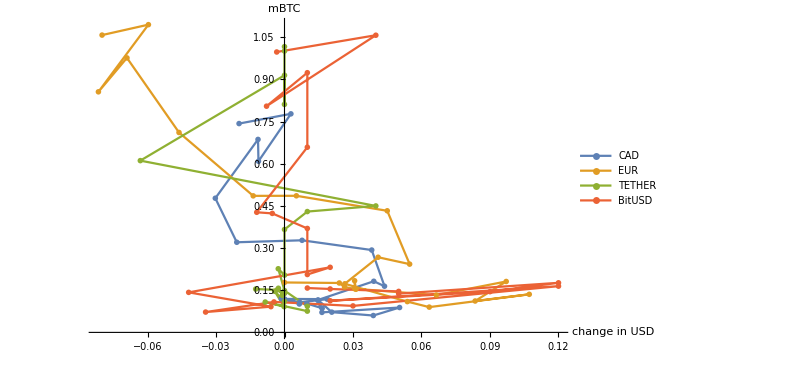

```mathematica
ListPlot[{data3,data4,data5,data6},Joined->True, PlotRange->All,PlotLegends-> {"CAD","EUR","TETHER","BitUSD"}, PlotLabel->"", AxesLabel->{"change in USD","mBTC"},ImageSize->600,PlotMarkers->{●}]
```

{0.2,0.4,0.6,0.8,1.}

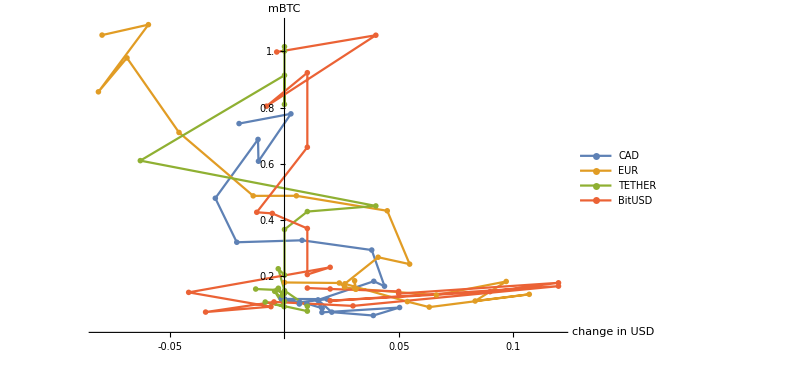

-Graphics-

```mathematica
ticks={-0.05,0.05,0.10};
ticks1={0.2,0.4,0.6,0.8,1.0}
a=ListPlot[{data3,data4,data5,data6},Joined->True, PlotRange->All,PlotLegends-> {"CAD","EUR","TETHER","BitUSD"}, PlotLabel->"", AxesLabel->{"change in USD","mBTC"},ImageSize->600,PlotMarkers->{●}, Ticks->{ticks,ticks1,Automatic}]
```

```mathematica
Export[NotebookDirectory[]<>"newGraph.pdf",a,"PDF"];
```